```mathematica
Needs["NDSolve`FEM`"]
region=Line[{{0},{100}}];
includePoints={{10},{20}, {30}, {40}, {50}};
mesh=ToElementMesh[region,"IncludePoints"->includePoints,"MaxCellMeasure"->0.0008]
```

ElementMesh[{{0.,100.}},{LineElement[<125000>]}]

```mathematica
vars={c[t,x],t,{x}};
pars=<|"DiffusionCoefficient"->910,"MassConvectionVelocity"->{162}|>;
```

```mathematica
RegularizedDeltaPoint[g_,X_List,Xs_List]:=Piecewise[{{Times@@Thread[1/(4 g) (1+Cos[π/(2 g) (X-Xs)])],And@@Thread[RealAbs[X-Xs]≤2 g]},{0,True}}]
```

```mathematica
Subscript[h,mesh]=Sqrt[Min[mesh["MeshElementMeasure"]]];
Subscript[gamma,reg]=Subscript[h,mesh]/2;
```

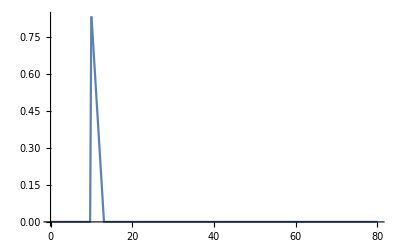

```mathematica
temp=RegularizedDeltaPoint[Subscript[gamma,reg],{x},includePoints[[1]]];
Plot[temp,{x,0,80}]
```

```mathematica
parameters={kappa->{{1}},v1->100,gamma->Subscript[gamma,reg],Qp->1.5};
pde={Derivative[1,0][c][t,x]+Inactive[Div][(-kappa).Inactive[Grad][c[t,x],{x}],{x}]+{v1}.Inactive[Grad][c[t,x],{x}]-Qp*RegularizedDeltaPoint[gamma,{x},{10}]-Qp*RegularizedDeltaPoint[gamma,{x},{20}]- Qp*RegularizedDeltaPoint[gamma,{x},{30}]-Qp*RegularizedDeltaPoint[gamma,{x},{40}]-Qp*RegularizedDeltaPoint[gamma,{x},{50}]
==0,c[0,x]==0}/.parameters;

tEnd=2;
cfun=NDSolveValue[pde,c,{t,0,tEnd},{x}∈mesh];
```

$Aborted

```mathematica
Manipulate[Plot[cfun[t,x],{x}∈region,PlotRange->{{0,100},{0,5}}],{t,0,tEnd}]
```

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

```mathematica
`
```